```mathematica
Clear["Global`*"]
```

```mathematica
(* g is an increasing function of z. *)
eq1=Collect[Simplify[(1-z)*gy+z*gz-g/.{gy->Qdg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gy^2+(g-(1-z)*gy)^2-z*g2/.{gy->Qdg*g+1-g}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}]
```

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

{-(Qcg-Qdg) (1-3 g+g Qdg) (1-g+g Qdg),-2-4 Qcg+8 g Qcg+5 Qdg-8 g Qdg+2 Qcg Qdg-8 g Qcg Qdg-2 Qdg^2+8 g Qdg^2+2 g Qcg Qdg^2-2 g Qdg^3+4 Qcg z-6 g Qcg z-4 Qdg z+6 g Qdg z-2 Qcg Qdg z+8 g Qcg Qdg z+2 Qdg^2 z-8 g Qdg^2 z-2 g Qcg Qdg^2 z+2 g Qdg^3 z}

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0>0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

True

True

```mathematica
eqa=g*(2-Qdg)-1;
eqb=((z-z^2)*(Qdg*g+1-g)^2+(g-(1-z)*(Qdg*g+1-g))^2)*(Qcg-Qdg);
H=eqb-eqa;
H=H/.{g->g[z]};
{K0,K1}=CoefficientList[D[H,z],g'[z]]/.{g[z]->g}
```

{2 (Qcg-Qdg) (g-(1-g+g Qdg) (1-z))-2 g (Qcg-Qdg) (g-(1-g+g Qdg) (1-z))+2 g (Qcg-Qdg) Qdg (g-(1-g+g Qdg) (1-z))+(Qcg-Qdg) (1-g+g Qdg)^2 (1-2 z),-2+Qdg+2 (Qcg-Qdg) (g-(1-g+g Qdg) (1-z))-2 (Qcg-Qdg) (g-(1-g+g Qdg) (1-z)) (-1+z)+2 (Qcg-Qdg) Qdg (g-(1-g+g Qdg) (1-z)) (-1+z)-2 (Qcg-Qdg) (1-g+g Qdg) (z-z^2)+2 (Qcg-Qdg) Qdg (1-g+g Qdg) (z-z^2)}

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&eqa==eqb&&1≥z≥0,FullSimplify@Reduce[K0>0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&eqa== eqb&&1≥z≥0,FullSimplify@Reduce[K1<0]]
```

True

True

```mathematica
Simplify[K1]
Hh=Simplify[Expand[eqb-eqa]]
```

-2-2 (-1+4 g) Qdg^2 (-1+z)+2 g Qdg^3 (-1+z)+Qdg (5-8 g-4 z+6 g z)-2 Qcg ((-2+Qdg) (-1+z)+g (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z))

1+Qcg-Qdg+g (-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))-Qcg z+Qdg z-g^2 (Qcg-Qdg) (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z)

```mathematica
U=FullSimplify[-2*(Qcg-Qdg)g (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z)]
myK=FullSimplify[K1-U]
myH=FullSimplify[2*Hh-g*U]
```

-2 g (Qcg-Qdg) (-4+(-4+Qdg) Qdg (-1+z)+3 z)

(-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))

-2 (-1+Qdg+Qcg (-1+z)-Qdg z+g (-2+Qdg) (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z))

```mathematica
mysol=FullSimplify[Expand[K1*g-2Hh]]
```

g (-2+Qdg) (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z)+2 (-1+Qdg+Qcg (-1+z)-Qdg z)

```mathematica
FullSimplify[mysol-g(2-Qdg)(1+2(Qcg-Qdg)(1-z))+2(1+(Qcg-Qdg)(1-z))]
```

0

```mathematica
mysol=FullSimplify[Expand[K1*(g(2-Qdg)-1)-4*Hh]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g≥0&&g*(2-Qdg)≥ 1&&1>Qcg>0&&1>Qdg>0&&Qcg>Qdg&&1≥z≥0,FullSimplify@Reduce[FullSimplify[mysol]<0]]
```

(1+g (-2+Qdg)) (-2+Qdg (-1-2 Qcg (1+g (-2+Qdg))+2 (Qdg+g (-2+Qdg) Qdg)))+2 (Qcg-Qdg) (Qdg+g (-1+2 (-2+Qdg) Qdg+g (-3+Qdg) (-1+Qdg) Qdg)) z

2 (-Qcg+Qdg) (Qdg+g (-1+2 (-2+Qdg) Qdg+g (-3+Qdg) (-1+Qdg) Qdg)) z>(1+g (-2+Qdg)) (-2+Qdg (-1-2 Qcg (1+g (-2+Qdg))+2 (1+g (-2+Qdg)) Qdg))||(Qdg>Root[-g+(1-4 g+3 g^2) #1+(2 g-4 g^2) #1^2+g^2 #1^3&,1]&&2 (-Qcg+Qdg) (Qdg+g (-1+2 (-2+Qdg) Qdg+g (-3+Qdg) (-1+Qdg) Qdg)) z<(1+g (-2+Qdg)) (-2+Qdg (-1-2 Qcg (1+g (-2+Qdg))+2 (1+g (-2+Qdg)) Qdg)))

```mathematica
Collect[Expand[g(2-Q)*(1+2*Δ*x)-2(1+Δ*x)],Δ]
```

-2+2 g-g Q+(-2 x+4 g x-2 g Q x) Δ

```mathematica
Assuming[1≥g≥0&&g*(2-Q)≥ 1&&Δ>0&&1>Q>0&&1≥x≥0,FullSimplify@Reduce[-2 x+4 g x-2 g Q x<0]]
```

False

```mathematica
FullSimplify[-2 x+4 g x-2 g Q x]
```

-2 (x+g (-2+Q) x)

```mathematica
Expand[3 g (-2+Qdg) (1+2 Δ x)+2 (1+Δx)]
```

2-6 g+3 g Qdg-12 g x Δ+6 g Qdg x Δ+2 Δx

```mathematica
FullSimplify[1+Qcg-Qdg+g (-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))-Qcg z+Qdg z]
```

```mathematica
1+g (-2+Qdg) (1+2( Qcg -Qdg)(1-z))+(Qcg-Qdg )(1- z)
```

1+g (-2+Qdg) (1+2 (Qcg-Qdg) (1-z))+(Qcg-Qdg) (1-z)

```mathematica
FullSimplify[g (-2+Qdg) (2 (Qcg-Qdg) (1-z))+(Qcg-Qdg) (1-z)]
```

(1+2 g (-2+Qdg)) (-Qcg+Qdg) (-1+z)

```mathematica
FullSimplify[g(Qdg-2)(1+2(Qcg-Qdg)(1-z))-2+2g(2-Qdg)+2(2g(2-Qdg)-1)(Qcg-Qdg)(1-z)]
```

g (-2+Qdg) (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z)+2 (-1+Qdg+Qcg (-1+z)-Qdg z)

```mathematica
U2=-(1+Qcg-Qdg+g (-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))-Qcg z+Qdg z)
```

-1-Qcg+Qdg-g (-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))+Qcg z-Qdg z

```mathematica
U=-2g (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z)(Qcg-Qdg)
```

-2 g (Qcg-Qdg) (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z)

```mathematica
FullSimplify[ (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z)]
```

-4+(-4+Qdg) Qdg (-1+z)+3 z

```mathematica
tester=FullSimplify[K1-U]
```

(-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))

```mathematica
test=FullSimplify[Expand[tester+U2/g]]
```

(-1+Qdg+Qcg (-1+z)-Qdg z)/g

```mathematica
FullSimplify[(1-2 Qcg (-1+z)+2 Qdg (-1+z))+g^2 (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z)]
```

(-1+g^2) (-1+2 Qcg (-1+z)-2 Qdg (-1+z))

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[g (-2+Qdg) (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z)+2 (-1+Qdg+Qcg (-1+z)-Qdg z)<0]]
```

g (-2+Qdg) (-1+2 Qdg+2 Qcg (-1+z)-2 Qdg z)+2 (-1+Qdg+Qcg (-1+z)-Qdg z)<0

```mathematica
Expand[testk]
```

-2-4 Qcg+5 Qdg-8 g Qdg+2 Qcg Qdg-2 Qdg^2+8 g Qdg^2-2 g Qdg^3-2 g Qcg U+4 Qcg z-4 Qdg z+6 g Qdg z-2 Qcg Qdg z+2 Qdg^2 z-8 g Qdg^2 z+2 g Qdg^3 z

```mathematica
tester=Simplify[testk+(g*(2-Qdg)- 1)*testh]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[tester<0]]
```

-2-4 Qcg+8 g Qcg+5 Qdg-8 g Qdg+2 Qcg Qdg-8 g Qcg Qdg-2 Qdg^2+8 g Qdg^2+2 g Qcg Qdg^2-2 g Qdg^3+4 Qcg z-6 g Qcg z-4 Qdg z+6 g Qdg z-2 Qcg Qdg z+8 g Qcg Qdg z+2 Qdg^2 z-8 g Qdg^2 z-2 g Qcg Qdg^2 z+2 g Qdg^3 z-(1+g (-2+Qdg)) (1+Qcg-Qdg+g (-2+Qdg) (1-2 Qcg (-1+z)+2 Qdg (-1+z))-Qcg z+Qdg z-g^2 (Qcg-Qdg) (-4-4 Qdg (-1+z)+Qdg^2 (-1+z)+3 z))

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥1 &&Hh==0&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[K1< 0]]
```

True

```mathematica
f1=(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg));
f2=2 (Qcg-Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z;
```

```mathematica
FullSimplify[Expand[K1]]
```

(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z

```mathematica
FullSimplify[K1]
Hh=FullSimplify[H/.{g[z]->g}]
```

(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
test=FullSimplify[K1*((Qdg-2)-1)-Hh]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[test<0]]
```

-1-g (-2+Qdg)+(-3+Qdg) ((-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z)-(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

$Aborted

```mathematica
Simplify[Expand[((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)]]
```

1+g^2 (4+4 Qdg (-1+z)-Qdg^2 (-1+z)-3 z)-2 g (-2+Qdg) (-1+z)-z

```mathematica
FullSimplify[eq1]
FullSimplify[eq2]
```

1+g (-2+Qdg)+g2 (Qcg-Qdg) z

(g+(1+g (-1+Qdg)) (-1+z))^2-g2 z-(1+g (-1+Qdg))^2 (-1+z) z

```mathematica
FullSimplify[k1]
FullSimplify[h]
```

(-2+Qdg) (1+2 Qcg (1+g (-2+Qdg))-2 (Qdg+g (-2+Qdg) Qdg))+2 (-Qcg+Qdg) (-2+g (-3+Qdg) (-1+Qdg)+Qdg) z

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
FullSimplify[Expand[((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)]]
```

1+g^2 (4-(-4+Qdg) Qdg (-1+z)-3 z)-2 g (-2+Qdg) (-1+z)-z

```mathematica
L1=1+2 (Qcg-Qdg) (1+g (-2+Qdg))
```

1+2 (1+g (-2+Qdg)) (Qcg-Qdg)

```mathematica
k3=FullSimplify[(g*(2-Qdg)- 1)*k1-h]
```

(1+g (-2+Qdg)) (1-Qcg (1+g (-2+Qdg)) (-3+2 Qdg)+(-2+Qdg) Qdg (2+g (-3+2 Qdg)))+(Qcg-Qdg) (-3+2 Qdg+g (-1+Qdg) (-10+4 Qdg+g (-3+Qdg) (-3+2 Qdg))) z

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&h== 0&&1>Qcg>Qdg>0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

True

```mathematica
k1
```

-2-4 Qcg+8 g Qcg+5 Qdg-8 g Qdg+2 Qcg Qdg-8 g Qcg Qdg-2 Qdg^2+8 g Qdg^2+2 g Qcg Qdg^2-2 g Qdg^3+4 Qcg z-6 g Qcg z-4 Qdg z+6 g Qdg z-2 Qcg Qdg z+8 g Qcg Qdg z+2 Qdg^2 z-8 g Qdg^2 z-2 g Qcg Qdg^2 z+2 g Qdg^3 z

```mathematica
(* Pij and Qij for the simple standing norm. *)
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥ĝ≥0,FullSimplify@Reduce[Qcg≥Qdg]] (* If g=0 or 1 then Qcg = Qdg. *)
```

g∈ℝ&&(e+g ϵ<e g||0≤g≤1||e+g ϵ>1+e g)

```mathematica
Together[2-Qcg]
```

(-2 e+2 e^2+3 e g-4 e^2 g-e g^2+2 e^2 g^2-2 g ϵ+2 e g ϵ+g^2 ϵ-2 e g^2 ϵ+g ϵ^2)/((-e+e g-g ϵ) (1-e+e g-g ϵ))

```mathematica
Together[G*(2-Qcg)-1/.{g->G*λ+1-λ}]
```

(ϵ-G ϵ-ϵ^2+G ϵ^2+e λ-2 e G λ+e G^2 λ-ϵ λ-2 e ϵ λ+G ϵ λ+4 e G ϵ λ-2 e G^2 ϵ λ+2 ϵ^2 λ-3 G ϵ^2 λ+G^2 ϵ^2 λ-e^2 λ^2-e G λ^2+4 e^2 G λ^2+2 e G^2 λ^2-5 e^2 G^2 λ^2-e G^3 λ^2+2 e^2 G^3 λ^2+2 e ϵ λ^2+G ϵ λ^2-6 e G ϵ λ^2-2 G^2 ϵ λ^2+6 e G^2 ϵ λ^2+G^3 ϵ λ^2-2 e G^3 ϵ λ^2-ϵ^2 λ^2+2 G ϵ^2 λ^2-G^2 ϵ^2 λ^2)/((-1+ϵ+e λ-e G λ-ϵ λ+G ϵ λ) (ϵ+e λ-e G λ-ϵ λ+G ϵ λ))

```mathematica
FullSimplify[(ϵ-G ϵ-ϵ^2+G ϵ^2+e λ-2 e G λ+e G^2 λ-ϵ λ-2 e ϵ λ+G ϵ λ+4 e G ϵ λ-2 e G^2 ϵ λ+2 ϵ^2 λ-3 G ϵ^2 λ+G^2 ϵ^2 λ-e^2 λ^2-e G λ^2+4 e^2 G λ^2+2 e G^2 λ^2-5 e^2 G^2 λ^2-e G^3 λ^2+2 e^2 G^3 λ^2+2 e ϵ λ^2+G ϵ λ^2-6 e G ϵ λ^2-2 G^2 ϵ λ^2+6 e G^2 ϵ λ^2+G^3 ϵ λ^2-2 e G^3 ϵ λ^2-ϵ^2 λ^2+2 G ϵ^2 λ^2-G^2 ϵ^2 λ^2)]
```

-(-1+G) (ϵ^2 (-1+λ) (1+(-1+G) λ)+ϵ (1+(-1+G) λ) (1+2 e (-1+G) λ-G λ)-e (-1+G) λ (1-G λ+e (-1+2 G) λ))

```mathematica
{c,b,a}=CoefficientList[ -(ϵ^2 (-1+λ) (1+(-1+G) λ)+ϵ (1+(-1+G) λ) (1+2 e (-1+G) λ-G λ)-e (-1+G) λ (1-G λ+e (-1+2 G) λ))/.{G->G-1},G]
```

{-ϵ-ϵ^2 (-1+λ)-2 e λ+ϵ λ+4 e ϵ λ+2 ϵ^2 (-1+λ) λ-2 e λ^2+6 e^2 λ^2+2 ϵ λ^2-8 e ϵ λ^2,e λ-2 e ϵ λ-ϵ^2 (-1+λ) λ+3 e λ^2-7 e^2 λ^2-3 ϵ λ^2+8 e ϵ λ^2,-e λ^2+2 e^2 λ^2+ϵ λ^2-2 e ϵ λ^2}

```mathematica
(ϵ^2 (-1+λ) (1+(-1+G) λ)+ϵ (1+(-1+G) λ) (1+2 e (-1+G) λ-G λ)-e (-1+G) λ (1-G λ+e (-1+2 G) λ))/.{G->1}
```

```mathematica
FullSimplify[g^2 (-1+ϵ)^2 ϵ^2+e^3 (-1+g)^2 (-1+2 ϵ)+e (-1+g) ϵ (-ϵ+g (-2+3 ϵ))-e^2 (-1+g) (1-ϵ (2+ϵ)+g (-1+3 ϵ^2))]
```

g^2 (-1+ϵ)^2 ϵ^2+e^3 (-1+g)^2 (-1+2 ϵ)+e (-1+g) ϵ (-ϵ+g (-2+3 ϵ))-e^2 (-1+g) (1-ϵ (2+ϵ)+g (-1+3 ϵ^2))

```mathematica
Pcg=(ϵ*g)/(ϵ*g+e*(1-g));
Pdg=((1-ϵ)*g)/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
mydiff=D[z*Qcg+(1-z)*Qdg,g];
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>Qdg>0&&1>z>0,FullSimplify@Reduce[mydiff*g+z*Qcg+(1-z)*Qdg-2<0]]
```

$Aborted

```mathematica
Solve[g==z*Qcg*g+(1-z)*Qdg*g+1-g,g]
```

{{g→1},{g→(2 e-3 e^2-ϵ+2 e ϵ-√((-2 e+3 e^2+ϵ-2 e ϵ)^2-4 (e-e^2) (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2)))/(2 (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2))},{g→(2 e-3 e^2-ϵ+2 e ϵ+√((-2 e+3 e^2+ϵ-2 e ϵ)^2-4 (e-e^2) (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2)))/(2 (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2))}}

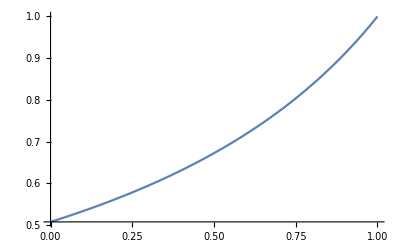

```mathematica
Plot[(2 e-3 e^2-ϵ+2 e ϵ-√((-2 e+3 e^2+ϵ-2 e ϵ)^2-4 (e-e^2) (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2)))/(2 (e-3 e^2+e^2 z-ϵ+4 e ϵ-2 e z ϵ-ϵ^2+z ϵ^2))/.{e->0.01,ϵ->0.98},{z,0,1}]
```

```mathematica
Solve[g ϵ (-1+g M z+2 e (-1+g) (-1+z+g M z)+(z-g (-1+z+g M z)) ϵ)==e (-1+g) (-1+e+g M z+e g (-1+z+(-1+g) M z)),M]
```

{{M→(-e+e^2+e g-2 e^2 g+e^2 g^2+e^2 g z-e^2 g^2 z-g ϵ+2 e g ϵ-2 e g^2 ϵ-2 e g z ϵ+2 e g^2 z ϵ+g^2 ϵ^2+g z ϵ^2-g^2 z ϵ^2)/(g z (-e+e^2+e g-2 e^2 g+e^2 g^2-g ϵ+2 e g ϵ-2 e g^2 ϵ+g^2 ϵ^2))}}

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>Qcg>Qdg>0&&1>z>0,FullSimplify@Reduce[mydiff>0]]
```

(e+ϵ==1&&2 g<1)||(g<√(((-1+e) e (-1+ϵ) ϵ)/((e-ϵ)^2 (-1+e+ϵ)^2))+((-1+e) e)/((e-ϵ) (-1+e+ϵ))&&e+ϵ<1)||(e+ϵ>1&&g<((-1+e) e+√((-1+e) e (-1+ϵ) ϵ))/((e-ϵ) (-1+e+ϵ)))

```mathematica
FullSimplify[(D[Qcg-Qdg,g])*g+(Qcg-Qdg)-1]
```

(-(-1+e)^2 e^2 (-1+g)^2+e g (-2+2 e+2 g-3 e g) ϵ+g (-g+e (2+e (-2+3 g))) ϵ^2+(1-2 e) g^2 ϵ^3)/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
(* Find the cubic numerator of f = πz - πy (given a postive denominator). For public assessment. *)
gb=λ*β+(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
numdomzy=NumeratorDenominator[Together[r(2*g-1-Qdg*g)-g]];
polyzy = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0&&1>λ>0&&1≥β≥ 0,FullSimplify@Sign[numdomzy[[2]]]]*numdomzy[[1]];
{c0,c1,c2,c3}=Simplify[CoefficientList[polyzy,g]]
```

{-r (e^2 (-1+β λ)^2+β ϵ λ (-1+β ϵ λ)-e (-1+β λ) (-1+2 β ϵ λ)) Sign[(-1+e-e g+g ϵ+(g-β) (e-ϵ) λ) (e-e g+g ϵ+(g-β) (e-ϵ) λ)],(e (-1+β λ) (-1+2 β ϵ λ)+e^2 (-1+β λ) (1-β λ+r (-4+2 λ+3 β λ))+ϵ (r-r (1+2 β (1+ϵ)) λ+r β (β+2 ϵ+β ϵ) λ^2+β λ (1-β ϵ λ))-e r (3-λ-3 β λ+β^2 λ^2+ϵ (2-2 (1+4 β) λ+4 β (1+β) λ^2))) Sign[(-1+e-e g+g ϵ+(g-β) (e-ϵ) λ) (e-e g+g ϵ+(g-β) (e-ϵ) λ)],-(-1+λ) (e^2 (2-2 β λ+r (-6+λ+6 β λ))+ϵ (1-2 β ϵ λ+r (-2+2 β λ+ϵ (-1+λ+2 β λ)))-e (1+2 ϵ-4 β ϵ λ+r (-3+2 β λ+2 ϵ (-3+λ+4 β λ)))) Sign[(-1+e-e g+g ϵ+(g-β) (e-ϵ) λ) (e-e g+g ϵ+(g-β) (e-ϵ) λ)],(e-ϵ) (e (-1+3 r)+ϵ-r (1+ϵ)) (-1+λ)^2 Sign[(-1+e-e g+g ϵ+(g-β) (e-ϵ) λ) (e-e g+g ϵ+(g-β) (e-ϵ) λ)]}

```mathematica
FullSimplify[D[Qcg-Qdg,g]]
```

-((e-ϵ)^2 ((-1+e) e (-1+g)^2+g^2 ϵ-g^2 ϵ^2))/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
Collect[((-1+e) e (-1+g)^2+g^2 ϵ-g^2 ϵ^2),g]
```

(-1+e) e-2 (-1+e) e g+g^2 ((-1+e) e+ϵ-ϵ^2)

```mathematica
FullSimplify[{c,b,a}]
```

{(-1+ϵ) ϵ-2 e λ+(1+4 e-3 ϵ) ϵ λ+2 (1-3 e+ϵ) (-e+ϵ) λ^2,λ (e+3 e λ-7 e^2 λ+e ϵ (-2+8 λ)+ϵ (ϵ-(3+ϵ) λ)),(-1+2 e) (e-ϵ) λ^2}

```mathematica
Expand[c]
```

-ϵ+ϵ^2-2 e λ+ϵ λ+4 e ϵ λ-3 ϵ^2 λ-2 e λ^2+6 e^2 λ^2+2 ϵ λ^2-8 e ϵ λ^2+2 ϵ^2 λ^2

```mathematica
FullSimplify[-ϵ+ϵ^2-2 e λ+ϵ λ+4 e ϵ λ-3 ϵ^2 λ-e λ^2+4 e^2 λ^2+ϵ λ^2-6 e ϵ λ^2+2 ϵ^2 λ^2]
```

```mathematica
(-1+ϵ) ϵ-2 e λ+(1+4 e-3 ϵ) ϵ λ+(-e+ϵ) (1-4 e+2 ϵ) λ^2/.{λ->1}
```

```mathematica
FullSimplify[-2 e+(1+4 e-3 ϵ) ϵ+(-1+ϵ) ϵ+(-e+ϵ) (1-4 e+2 ϵ)]
```

e (-3+4 e-2 ϵ)+ϵ

```mathematica
Together[G*(2-Qcg)-1]
```

{{G→1},{G→1/(2 (e λ^2-2 e^2 λ^2-ϵ λ^2+2 e ϵ λ^2))(e λ-2 e ϵ λ+ϵ^2 λ+e λ^2-3 e^2 λ^2-ϵ λ^2+4 e ϵ λ^2-ϵ^2 λ^2-√(-4 (e λ^2-2 e^2 λ^2-ϵ λ^2+2 e ϵ λ^2) (ϵ-ϵ^2+e λ-ϵ λ-2 e ϵ λ+2 ϵ^2 λ-e^2 λ^2+2 e ϵ λ^2-ϵ^2 λ^2)+(-e λ+2 e ϵ λ-ϵ^2 λ-e λ^2+3 e^2 λ^2+ϵ λ^2-4 e ϵ λ^2+ϵ^2 λ^2)^2))},{G→1/(2 (e λ^2-2 e^2 λ^2-ϵ λ^2+2 e ϵ λ^2))(e λ-2 e ϵ λ+ϵ^2 λ+e λ^2-3 e^2 λ^2-ϵ λ^2+4 e ϵ λ^2-ϵ^2 λ^2+√(-4 (e λ^2-2 e^2 λ^2-ϵ λ^2+2 e ϵ λ^2) (ϵ-ϵ^2+e λ-ϵ λ-2 e ϵ λ+2 ϵ^2 λ-e^2 λ^2+2 e ϵ λ^2-ϵ^2 λ^2)+(-e λ+2 e ϵ λ-ϵ^2 λ-e λ^2+3 e^2 λ^2+ϵ λ^2-4 e ϵ λ^2+ϵ^2 λ^2)^2))}}

```mathematica
(* z=1 implies that g=gz=1. *)
FullSimplify[Qcg*g^2+Qdg*(g-g^2)+1-2*g]
```

1-2 g+(g ĝ (e (-1+e-e g)+2 e g ϵ-g ϵ^2+(e-ϵ) (1+e (-1+g)-(1+g) ϵ) ĝ))/((-e+(e-ϵ) ĝ) (1-e+(e-ϵ) ĝ))

```mathematica
NumeratorDenominator[Together[r*(2*g-Qdg*g-1)-g]]
```

{e g-e^2 g+e r-e^2 r-2 e g r+2 e^2 g r-e g ĝ+2 e^2 g ĝ-e r ĝ+2 e^2 r ĝ+3 e g r ĝ-5 e^2 g r ĝ+g ϵ ĝ-2 e g ϵ ĝ+r ϵ ĝ-2 e r ϵ ĝ-2 g r ϵ ĝ+4 e g r ϵ ĝ-e^2 g (ĝ)^2-e^2 r (ĝ)^2-e g r (ĝ)^2+3 e^2 g r (ĝ)^2+2 e g ϵ (ĝ)^2+2 e r ϵ (ĝ)^2+g r ϵ (ĝ)^2-4 e g r ϵ (ĝ)^2-g ϵ^2 (ĝ)^2-r ϵ^2 (ĝ)^2+g r ϵ^2 (ĝ)^2,(-e+e ĝ-ϵ ĝ) (1-e+e ĝ-ϵ ĝ)}

```mathematica
FullSimplify[e g-e^2 g+e r-e^2 r-2 e g r+2 e^2 g r-e g ĝ+2 e^2 g ĝ-e r ĝ+2 e^2 r ĝ+3 e g r ĝ-5 e^2 g r ĝ+g ϵ ĝ-2 e g ϵ ĝ+r ϵ ĝ-2 e r ϵ ĝ-2 g r ϵ ĝ+4 e g r ϵ ĝ-e^2 g (ĝ)^2-e^2 r (ĝ)^2-e g r (ĝ)^2+3 e^2 g r (ĝ)^2+2 e g ϵ (ĝ)^2+2 e r ϵ (ĝ)^2+g r ϵ (ĝ)^2-4 e g r ϵ (ĝ)^2-g ϵ^2 (ĝ)^2-r ϵ^2 (ĝ)^2+g r ϵ^2 (ĝ)^2]
```

(-1+e) e (-r+g (-1+2 r))+ĝ (-e (g+r-2 e r-3 g r+e g (-2+5 r))+(-1+2 e) (-r+g (-1+2 r)) ϵ+(e-ϵ) (e (-r+g (-1+3 r))+r ϵ-g (r+(-1+r) ϵ)) ĝ)

```mathematica
FullSimplify[Qdg*g+1-g-Qcg*g2-Qdg*(g-g2)-1+g]
```

-((-1+g) g2 (e-ϵ)^2 ĝ)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Together[(Qcg-Qdg)*(1-λ)]
```

1/((-e+e g-g ϵ) (1-e+e g-g ϵ))(-e λ+e^2 λ+e g λ-2 e^2 g λ+e^2 g^2 λ-g ϵ λ+2 e g ϵ λ-2 e g^2 ϵ λ+g^2 ϵ^2 λ-e^2 ĝ+e^2 g ĝ+2 e ϵ ĝ-2 e g ϵ ĝ-ϵ^2 ĝ+g ϵ^2 ĝ+e^2 λ ĝ-e^2 g λ ĝ-2 e ϵ λ ĝ+2 e g ϵ λ ĝ+ϵ^2 λ ĝ-g ϵ^2 λ ĝ)

```mathematica
FullSimplify[(-e λ+e^2 λ+e g λ-2 e^2 g λ+e^2 g^2 λ-g ϵ λ+2 e g ϵ λ-2 e g^2 ϵ λ+g^2 ϵ^2 λ-e^2 ĝ+e^2 g ĝ+2 e ϵ ĝ-2 e g ϵ ĝ-ϵ^2 ĝ+g ϵ^2 ĝ+e^2 λ ĝ-e^2 g λ ĝ-2 e ϵ λ ĝ+2 e g ϵ λ ĝ+ϵ^2 λ ĝ-g ϵ^2 λ ĝ)]
```

(e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ) λ-(-1+g) (e-ϵ)^2 (-1+λ) ĝ

```mathematica
Solve[(1-gx)*((Rcg*g+1-g)*(1-λ)+λ)-gx*(1-Rcg)*g*(1-λ)==0,gx]
```

{{gx→1-g+g Rcg+g λ-g Rcg λ}}

```mathematica
(* Find the cubic numerator of f = πz - πy (given a postive denominator). *)
numdomzy=NumeratorDenominator[Together[r*(2*g-Qdg*g-1)-g]];
polyzy = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzy[[2]]]]*numdomzy[[1]];
{c0,c1,c2,c3}=Simplify[CoefficientList[polyzy,g]];
```

Set::shape: Lists {c0,c1,c2,c3} and {-r ((-1+e) e-(-1+2 e) (e-ϵ) ĝ+(e-ϵ)^2 (ĝ)^2) Sign[(-e+(e+Times[«2»]) ĝ) (1-e+(e+Times[«2»]) ĝ)],((-1+e) e (-1+2 r)+(e^2 (2+Times[«2»])+ϵ-2 r ϵ+e (-1+Times[«2»]+Times[«2»])) ĝ+(e-ϵ) (e (-1+Times[«2»])+ϵ-r (1+ϵ)) (ĝ)^2) Sign[(-e+(e+Times[«2»]) ĝ) (1-e+(e+Times[«2»]) ĝ)]} are not the same shape.

```mathematica
(* Prove that c0 > 0, c3 > 0, and c2 and c3 can't both be positive. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c0<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c3<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c1<0&&c2<0]]
```

True

True

False

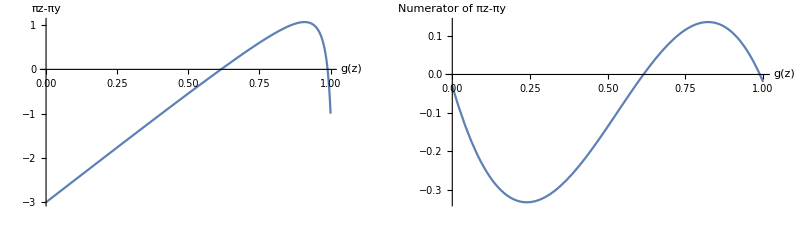

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(2*g-Qdg*g-1)-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πy"}],
Plot[Evaluate[polyzy//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πy"}]}]
```

```mathematica
(* Find the cubic numerator of f = πz - πx (given a postive denominator). *)
numdomzx=NumeratorDenominator[Together[r*(2*g-Qcg*g-1)+1-g]];
polyzx = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzx[[2]]]]*numdomzx[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx,g]];
```

```mathematica
(* The cubic's coefficients. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1<0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1>0&&a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[(a1>0&&a2<0&&a3>0)]]
```

True

True

True

«1 more identical outputs»

```mathematica
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&1>e1>0&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0<0]]
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&1>e1>0&&1>ϵ>0.5>e>0,FullSimplify@Reduce[(a1<0&&a2<0)]]
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&1>e1>0&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a2>0]]
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e*e1&&1>e1>0&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a3<0]]
```

True

ϵ>Root[3 e^2-6 e^3+3 e^4+(-3 e+4 e^2) #1+(1+e-4 e^2) #1^2+(-1+2 e) #1^3&,1]&&(3 e^2+ϵ-2 e (1+ϵ))/(e (-3+4 e-2 ϵ)+ϵ)<r<((e-ϵ) (-1+3 e-ϵ))/(e (-3+5 e-4 ϵ)+2 ϵ)

3 e (e+r)+ϵ+4 e r ϵ+ϵ^2<e+5 e^2 r+4 e ϵ+2 r ϵ

True

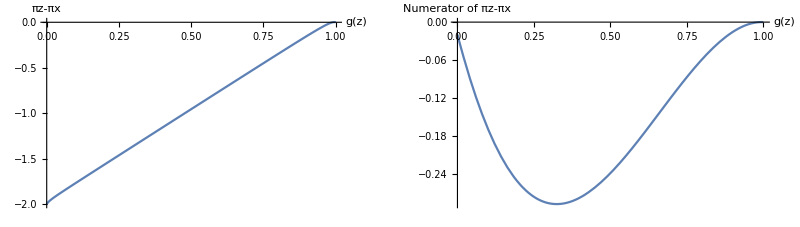

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(2*g-Qcg*g-1)+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πx"}],
Plot[Evaluate[polyzx//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πx"}]}]
```

```mathematica
(* Show that df/dz = -dg/dz and df/dg = -1 at z=0,1 and g=1. *)
Simplify[D[r*(2*g-1-Qcg*g)+1-g/.{g->g[z]},z]/.{g[z]->1}]
Simplify[D[r*(2*g-1-Qcg*g)+1-g,g]/.{g->1}]
```

-g'[z]

-1

```mathematica
(* Prove that pix=piz on the y-axis. *)
eq1=Collect[Simplify[(1-z)*gx+z*gz-g/.{gx->Qcg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gx^2+(g-(1-z)*gx)^2-z*g2/.{gx->Qcg*g+1-g}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}];
```

1+g (-2+Qcg-Qcg z+Qdg z)+(Qcg-Qdg) ((g+(1+g (-1+Qcg)) (-1+z))^2-(1+g (-1+Qcg))^2 (-1+z) z)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1≥ Qcg≥ Qdg≥0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0==0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

3 g+2 Qcg==5||(Qcg≠1&&(g==2/(3-2 Qcg+√(-3+4 Qcg))||g==-2/(-3+2 Qcg+√(-3+4 Qcg))))||Qcg==Qdg

True

```mathematica
Solve[gx==Qcg*g+1-g&&gz==(Qcg-Qdg)*((1-z)*gx^2+z*gz^2)+Qdg*g+1-g&&g==(1-z)*gx+z*gz,{gx,gz}]
```

{}

```mathematica
FullSimplify[(1-gz)*(Qcg*g2+Qdg*(g-g2)+1-g)-gz*((1-Qcg)*g2+(1-Qdg)*(g-g2))]
```

1-gz+g2 Qcg+g (-1+Qdg)-g2 Qdg

```mathematica
FullSimplify[(1-z)*(Qcg*g+1-g)+z*(1-g+Qcg*g2+Qdg*(g-g2))-g]
```

1-2 g+g Qcg+(-g+g2) (Qcg-Qdg) z

```mathematica
FullSimplify[z*gz+(1-z)*gx-z*gz^2-(1-z)*gx^2]
```

gx+gx^2 (-1+z)-gx z-(-1+gz) gz z

```mathematica
(* Lemma A.3.3: On the line y=0, g=gx=gz=1 and thus piz=pix *)
```

```mathematica
FullSimplify[(1-z)*(Qcg*g+1-g)+z*(1-g+Qcg*g2+Qdg*(g-g2))-g]
```

1-2 g+g Qcg+(-g+g2) (Qcg-Qdg) z

```mathematica
FullSimplify[1-g+Qcg*g2+Qdg*(g-g2)-g]
```

```mathematica
FullSimplify[g2 (Qcg-Qdg)+g (-2+Qdg)-g*(Qcg-2)]
```

-(g-g2) (Qcg-Qdg)

```mathematica
FullSimplify[Qcg*g-g-g*(Qcg-2)-g]
```

0

```mathematica
Solve[Qcg-1==0,g]
```

{{g→1},{g→((-1+e) e)/(-e+e^2+ϵ-ϵ^2)}}

```mathematica
Assuming[r>1&&ϵ==(1-e)*(1-e1)+e1*e&&1≥e1>0&&1>ϵ>0.5>e>0&&1≥g>0&&1≥ Qcg≥ Qdg≥0&&h==0&&1≥z≥0,FullSimplify@Solve[Qcg-1==0,g]]
```

{{g→1},{g→((-1+e) e)/((e-ϵ) (-1+e+ϵ))}}

```mathematica
FullSimplify[(1-e2)*(1-e1)+e1*e2+e2-1]
```

e1 (-1+2 e2)